# Math 385 HW # 9

## Mario L. Gutierrez Abed

(1) Approximate the solution to the 1-D heat equation using the forward and backward Euler methods given the following criteria:
x ∈[0,1]       ;Δ x=0.1
t ∈[0,10]     ;Δ t = 0.005, 0.01, 0.05 (each value yields a new graph)
α=0.5
u(x_0,t_n) = 40. The temperature at all other points is 0 initially.

Solution:

							        Forward Difference Method

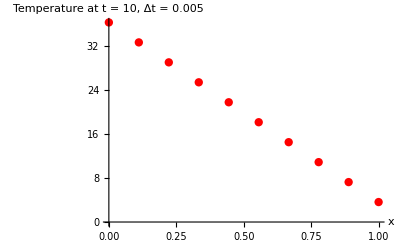

-Graphics-

-Graphics-

```mathematica
Δx=0.1;
Δt={0.005,0.01,0.05};
timesteps[s_]:=10/Δt⟦s⟧;
α=0.5;
λ[s_]:=α*Δt⟦s⟧/(Δx)^2;


FTCSmat[s_]:=({{1-2*λ[s], λ[s], 0, 0, 0, 0, 0, 0, 0, 0}, {λ[s], 1-2*λ[s], λ[s], 0, 0, 0, 0, 0, 0, 0}, {0, λ[s], 1-2*λ[s], λ[s], 0, 0, 0, 0, 0, 0}, {0, 0, λ[s], 1-2*λ[s], λ[s], 0, 0, 0, 0, 0}, {0, 0, 0, λ[s], 1-2*λ[s], λ[s], 0, 0, 0, 0}, {0, 0, 0, 0, λ[s], 1-2*λ[s], λ[s], 0, 0, 0}, {0, 0, 0, 0, 0, λ[s], 1-2*λ[s], λ[s], 0, 0}, {0, 0, 0, 0, 0, 0, λ[s], 1-2*λ[s], λ[s], 0}, {0, 0, 0, 0, 0, 0, 0, λ[s], 1-2*λ[s], λ[s]}, {0, 0, 0, 0, 0, 0, 0, 0, λ[s], 1-2*λ[s]}});
bdyvalues[s_]:=({{40*λ[s]}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}}); 
 solVec1=({{40}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
heatValues1={};
heatVecs1={};
For[i=1,i≤timesteps[1],i++,
solVec1=Dot[FTCSmat[1],solVec1]+bdyvalues[1];
AppendTo[heatVecs1,solVec1];
meh1=Table[heatVecs1⟦i⟧⟦j,1⟧,{j,1,10}];
AppendTo[heatValues1,meh1]
];
ListPlot[heatValues1⟦-1⟧,AxesLabel->{x,"Temperature at t = 10, Δt = 0.005"},PlotStyle->{Red,PointSize[0.015]},PlotRange->Automatic,DataRange->{0,1}]


solVec2=({{40}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
heatValues2={};
heatVecs2={};
For[i=1,i≤timesteps[2],i++,
solVec2=Dot[FTCSmat[2],solVec2]+bdyvalues[2];
AppendTo[heatVecs2,solVec2];
meh2=Table[heatVecs2⟦i⟧⟦j,1⟧,{j,1,10}];
AppendTo[heatValues2,meh2]
];
ListPlot[heatValues2⟦-1⟧,AxesLabel->{x,"Temperature at t = 10, Δt = 0.005"},PlotStyle->{Red,PointSize[0.015]},PlotRange->Automatic,DataRange->{0,1}]


solVec3=({{40}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
heatValues3={};
heatVecs3={};
For[i=1,i≤timesteps[3],i++,
solVec3=Dot[FTCSmat[3],solVec3]+bdyvalues[3];
AppendTo[heatVecs3,solVec3];
meh3=Table[heatVecs3⟦i⟧⟦j,1⟧,{j,1,10}];
AppendTo[heatValues3,meh3]
];
ListPlot[heatValues3⟦-1⟧,AxesLabel->{x,"Temperature at t = 10, Δt = 0.005"},PlotStyle->{Red,PointSize[0.015]},PlotRange->Automatic,DataRange->{0,1}]
```

There is an important observation to make here. The last plot looks like a mess because the increment of the time steps is too large relative to the increment on the x-coordinates, and this gives us a relatively high value for λ which in turn gives us very large numbers in our computations because our system is unstable. 
 

						           
						                            Backward Difference Method

```mathematica
BTCSmat[s_]:=({{1+2*λ[s], -λ[s], 0, 0, 0, 0, 0, 0, 0, 0}, {-λ[s], 1+2*λ[s], -λ[s], 0, 0, 0, 0, 0, 0, 0}, {0, -λ[s], 1+2*λ[s], -λ[s], 0, 0, 0, 0, 0, 0}, {0, 0, -λ[s], 1+2*λ[s], -λ[s], 0, 0, 0, 0, 0}, {0, 0, 0, -λ[s], 1+2*λ[s], -λ[s], 0, 0, 0, 0}, {0, 0, 0, 0, -λ[s], 1+2*λ[s], -λ[s], 0, 0, 0}, {0, 0, 0, 0, 0, -λ[s], 1+2*λ[s], -λ[s], 0, 0}, {0, 0, 0, 0, 0, 0, -λ[s], 1+2*λ[s], -λ[s], 0}, {0, 0, 0, 0, 0, 0, 0, -λ[s], 1+2*λ[s], -λ[s]}, {0, 0, 0, 0, 0, 0, 0, 0, -λ[s], 1+2*λ[s]}});

 solVec4=({{40}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
heatValues4={};
heatVecs4={};
For[i=1,i≤timesteps[1],i++,
solVec4=LinearSolve[BTCSmat[1],solVec4+bdyvalues[1]];
AppendTo[heatVecs4,solVec4];
meh4=Table[heatVecs4⟦i⟧⟦j,1⟧,{j,1,10}];
AppendTo[heatValues4,meh4]
];
ListPlot[heatValues4⟦-1⟧,AxesLabel->{x,"Temperature at t = 10, Δt = 0.005"},PlotStyle->{Red,PointSize[0.015]},PlotRange->Automatic,DataRange->{0,1}]



 solVec5=({{40}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
heatValues5={};
heatVecs5={};
For[i=1,i≤timesteps[2],i++,
solVec5=LinearSolve[BTCSmat[2],solVec5+bdyvalues[2]];
AppendTo[heatVecs5,solVec5];
meh5=Table[heatVecs5⟦i⟧⟦j,1⟧,{j,1,10}];
AppendTo[heatValues5,meh5]
];
ListPlot[heatValues5⟦-1⟧,AxesLabel->{x,"Temperature at t = 10, Δt = 0.005"},PlotStyle->{Red,PointSize[0.015]},PlotRange->Automatic,DataRange->{0,1}]


 solVec6=({{40}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
heatValues6={};
heatVecs6={};
For[i=1,i≤timesteps[3],i++,
solVec6=LinearSolve[BTCSmat[3],solVec6+bdyvalues[3]];
AppendTo[heatVecs6,solVec6];
meh6=Table[heatVecs6⟦i⟧⟦j,1⟧,{j,1,10}];
AppendTo[heatValues6,meh6]
];
ListPlot[heatValues6⟦-1⟧,AxesLabel->{x,"Temperature at t = 10, Δt = 0.005"},PlotStyle->{Red,PointSize[0.015]},PlotRange->Automatic,DataRange->{0,1}]
```

-Graphics-

-Graphics-

-Graphics-